```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NextGenAero/Vector8/GRA_OAG"]
```

/Users/brucesawhill/Desktop/NextGenAero/Vector8/GRA_OAG

```mathematica
FileNames[]
```

{DOMOAG.CSV,DOMOAG.sch,netairports,oagmma,rankseatpairlist}

```mathematica
FileFormat["DOMOAG.CSV"]
```

CSV

```mathematica
oagdata=Import["DOMOAG.CSV", "CSV"];
```

$Aborted

```mathematica
Dimensions[oagdata]
```

{1503906}

```mathematica
oagdata2=Drop[oagdata,-1];
```

```mathematica
Dimensions[oagdata2]
```

{1503905,8}

```mathematica
oagdata2>>oagmma;
```

```mathematica
oagdata2=<<oagmma;
```

```mathematica
oagdata2[[2]]
```

{198902,ABE,ATL,1315-1329,28,2996,3500,125}

How many seats over the entire data period?

```mathematica
Sum[oagdata2[[i,6]],{i,Length[oagdata2]}]
```

3284212365

What's the mean flight duration?

```mathematica
Sum[oagdata2[[i,5]] oagdata2[[i,8]],{i,Length[oagdata2]}]/Sum[oagdata2[[i,5]],{i,Length[oagdata2]}]//N
```

98.7622

What's the distribution of flight duration?

```mathematica
times=Table[0,{400}];
Do[If[oagdata2[[i,8]]≤400,times[[oagdata2[[i,8]]]]+=oagdata2[[i,5]]],{i,Length[oagdata2]}];
timebins=Table[Sum[times[[5j+i]],{i,1,5}],{j,0,79}]
```

{76975,314680,358986,533235,437151,822516,865074,1211047,1315484,1611292,1542245,2061389,1888976,2033243,1948353,1825986,1534370,1411375,1104640,1055155,996466,912926,820407,791767,654578,603527,572669,575081,546375,554816,531357,495772,431619,370541,320199,303549,251144,221603,187866,179910,168591,163728,151880,146870,150284,151741,142912,133908,111531,105873,94330,90400,89679,83191,75273,63324,58057,58258,55660,54598,52789,58769,65204,60571,55089,52364,44076,37573,31674,30619,23805,24205,21194,20816,20118,16034,13668,11221,8297,5302}

What's the mode of the flight time distribution?

```mathematica
Position[times,Max[times]]
```

{{60}}

```mathematica
labels=Flatten[Table[{"",ToString[i]},{i,10,400,10}]];
```

```mathematica
BarChart[timebins,ChartLabels->Placed[labels,Axis,Rotate[#,-Pi/2]&],PlotLabel->"OAG Flight Duration Histogram (mean = 98.7 min, mode = 60 min)",AxesLabel->{"Duration", "Number of Flights"}]
```

-Graphics-

What's the distribution of average plane size vs. number?  This isn't exactly right because some of the routes have zero passengers.

```mathematica
countuniquecities=Length[Union[Flatten[Table[{oagdata2[[i,2]],oagdata2[[i,3]]},{i,Length[oagdata2]}]]]]
```

1074

```mathematica
uniquepairs=Length[Union[Table[Sort[{oagdata2[[i,2]],oagdata2[[i,3]]}],{i,Length[oagdata2]}]]]
```

7750

```mathematica
tallypairs=Tally[Table[Sort[{oagdata2[[i,2]],oagdata2[[i,3]]}],{i,Length[oagdata2]}]];
```

```mathematica
tallypairs[[1]]
```

{{ABE,ATL},238}

```mathematica
stp=Sort[tallypairs];
```

```mathematica
seatstable=Sort[Table[{Sort[{oagdata2[[i,2]],oagdata2[[i,3]]}],oagdata2[[i,6]]},{i,Length[oagdata2]}]];
```

```mathematica
planestable=Sort[Table[{Sort[{oagdata2[[i,2]],oagdata2[[i,3]]}],oagdata2[[i,5]]},{i,Length[oagdata2]}]];
```

```mathematica
Take[seatstable,-10]
```

{{{WLB,WWP},168},{{WLB,WWP},168},{{WLB,WWP},168},{{WLB,WWP},182},{{WLB,WWP},182},{{WLB,WWP},182},{{WNA,WTL},180},{{WNA,WTL},216},{{WNA,WTL},234},{{WNA,WTL},243}}

```mathematica
Take[seatstable,10]
```

{{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},133}}

```mathematica
Take[planestable,10]
```

{{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},7}}

```mathematica
Length[seatstable]
```

1503905

```mathematica
Length[planestable]
```

1503905

```mathematica
Histogram[Union[Table[oagdata2[[i,6]]/oagdata2[[i,5]],{i,Length[oagdata2]}]],PlotLabel->"Histogram of Avg. Aircraft Capacity", AxesLabel->{"Seats","No. Aircraft"}]
```

-Graphics-

```mathematica
Floor[oagdata2[[-33,1]]/100]
```

2010

```mathematica
Take[seatstable,10]
```

{{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},76},{{ABE,ALB},133}}

```mathematica
Take[planestable,10]
```

{{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},4},{{ABE,ALB},7}}

```mathematica
Take[planestable,-4]
```

{{{WNA,WTL},20},{{WNA,WTL},24},{{WNA,WTL},26},{{WNA,WTL},27}}

```mathematica
Take[seatstable,-4]
```

{{{WNA,WTL},180},{{WNA,WTL},216},{{WNA,WTL},234},{{WNA,WTL},243}}

```mathematica
Plus[20,24,26,27]
```

97

```mathematica
Plus[549,417,447]
```

1413

```mathematica
Plus[180,216,234,243]
```

873

```mathematica
initcitypair=seatstable[[1,1]];
pairseatscounter=0;
j=1;
citypairseats=Table[0,{7750}];

Do[
{
If[seatstable[[i,1]]==initcitypair, 
pairseatscounter+=seatstable[[i,2]],
{
citypairseats[[j]]={initcitypair,pairseatscounter};
initcitypair=seatstable[[i,1]];
j++;
pairseatscounter=0
}
];
},{i,Length[seatstable]}
]
```

```mathematica
initcitypair=planestable[[1,1]];
pairplanescounter=0;
j=1;
citypairplanes=Table[0,{7750}];

Do[
{
If[planestable[[i,1]]==initcitypair, 
pairplanescounter+=planestable[[i,2]],
{
citypairplanes[[j]]={initcitypair,pairplanescounter};
initcitypair=planestable[[i,1]];
j++;
pairplanescounter=0
}
];
},{i,Length[planestable]}
]
```

```mathematica
citypairplanes[[2]]
citypairseats[[2]]
citypairplanes[[15]]
citypairseats[[15]]
```

{{ABE,ATL},6573}

{{ABE,ATL},573985}

{{ABE,EWR},3466}

{{ABE,EWR},116354}

```mathematica
Length[citypairplanes]
```

7750

```mathematica
citypairplanes2=DeleteCases[Table[If[citypairplanes[[i,2]]==0,0,citypairplanes[[i]]],{i,7750}],0];
```

```mathematica
Length[citypairplanes2]
```

7463

```mathematica
citypairseats2=DeleteCases[Table[If[citypairseats[[i,2]]==0,0,citypairseats[[i]]],{i,7750}],0];
```

```mathematica
Length[citypairseats2]
```

7463

```mathematica
seatsandplanes=Table[{citypairseats2[[i,2]],citypairseats2[[i,2]]/citypairplanes2[[i,2]]},{i,7463}]//N;
```

```mathematica
Take[seatsandplanes,10]
```

{{11324.,19.},{573985.,87.3247},{115458.,58.4597},{1140.,19.},{9733.,36.7283},{3796.,146.},{161928.,38.3807},{214478.,55.392},{150182.,30.3214},{344281.,91.8573}}

```mathematica
chunksumseats=0;
chunksumplanes=0;
counter=0;
Do[If[seatsandplanes[[i,1]]>10^2 && seatsandplanes[[i,1]]<10^(2+1),{chunksumseats+=citypairseats2[[i,2]],chunksumplanes+=citypairplanes2[[i,2]],counter++}],{i,7463}];
chunksumseats
chunksumplanes
chunksumseats/chunksumplanes//N
```

372353

25054

14.862

```mathematica
avgavg={{100,15},{1000,17},{10000,26},{100000,59},{1000000,114},{10000000,138}}
```

{{100,15},{1000,17},{10000,26},{100000,59},{1000000,114},{10000000,138}}

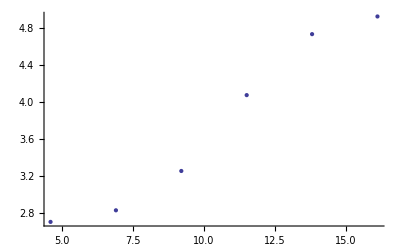

```mathematica
ListPlot[Log[avgavg]]
```

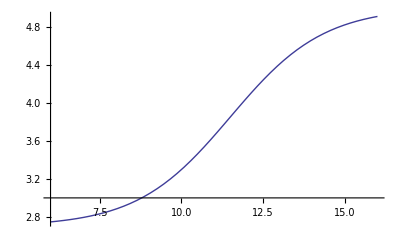

```mathematica
Plot[2.7+ 2.3 Exp[.7 (x-11.5)]/(1+Exp[.7 (x-11.5)]),{x,6,16}]
```

```mathematica
FindFit[Log[seatsandplanes],a+b Exp[c(x-d)]/(1 + Exp[c(x-d)]),{a,b,c,d},x,Method->NMinimize]
```

{a→2.88332,b→2.87962,c→0.412406,d→13.1774}

```mathematica
Exp[2.883+2.879]
```

317.984

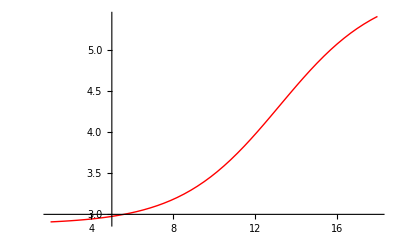

```mathematica
fit=Plot[2.88+2.88 Exp[.412(x-13.2)]/(1+Exp[.412(x-13.2)]),{x,2,18},PlotStyle->{Red,Thick}]
```

```mathematica
expfitplot=Plot[Exp[2.88+2.88 Exp[.412(Log[x]-13.2)]/(1+Exp[.412(Log[x]-13.2)])],{x,200,20000000},PlotStyle->{Red,Thick},PlotRange->{{0,20000000},{0,400}},Axes->True]
```

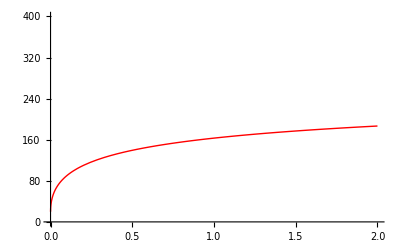

```mathematica
?FindFit
```

FindFit[data,expr,pars,vars] finds numerical values of the parameters pars that make expr give a best fit to data as a function of vars. The data can have the form {{x_1,y_1,…,f_1},{x_2,y_2,…,f_2},…}, where the number of coordinates x, y, … is equal to the number of variables in the list vars. The data can also be of the form {f_1,f_2,…}, with a single coordinate assumed to take values 1, 2, …. 
FindFit[data,{expr,cons},pars,vars] finds a best fit subject to the parameter constraints cons.

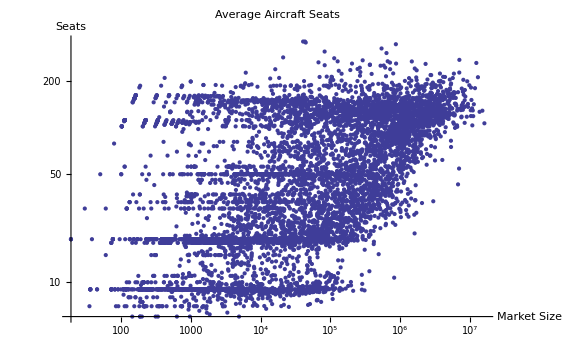

```mathematica
planescatter=ListLogLogPlot[seatsandplanes,PlotLabel->"Average Aircraft Seats",AxesLabel->{"Market Size","Seats"}]
```

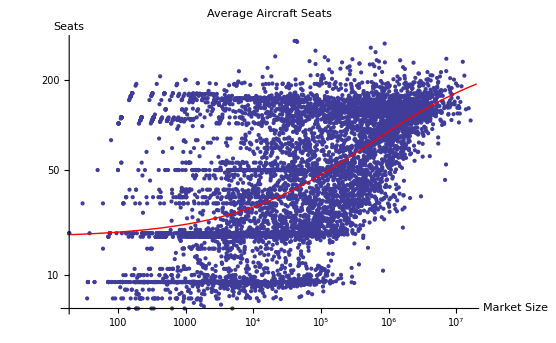

```mathematica
Show[planescatter,expfitplot]
```

```mathematica
citypairseats[[7749]]
```

{{WLB,WWP},1218}

```mathematica
citypairseats[[7750]]
```

{{WNA,WTL},873}

```mathematica
citypairseats[[7750]]={{"WNA","WTL"},873}
```

{{WNA,WTL},873}

```mathematica
citypairplanes[[7750]]={{"WNA","WTL"},97}
```

{{WNA,WTL},97}

```mathematica
rankseatpairlist=Sort[citypairseats,#2[[2]]<#1[[2]]&];
```

It turns out that the pair list has a bunch of zeroes in it, perhaps cities that were once ever flown.  This reduces the size down to 7463 from 7750.

```mathematica
Position[rankseatpairlist,0];
```

```mathematica
rankseatpairlist=Take[rankseatpairlist,7463];
```

```mathematica
rankseatpairlist>>rankseatpairlist;
```

```mathematica
rankseatpairlist=<<rankseatpairlist;
```

```mathematica
rankseatpairlist[[3]]
```

{{LAS,LAX},13904915}

```mathematica
Length[Union[Flatten[Table[rankseatpairlist[[i,1]],{i,Length[rankseatpairlist]}]]]]
```

1057

```mathematica
cumultable=Table[0,{7750}];
sum=0;
Do[
{sum+=rankseatpairlist[[i,2]];
cumultable[[i]]={i,sum/3284212365};
},{i,7750}
]
```

```mathematica
Take[cumultable,200]//N
```

{{1.,0.00496589},{2.,0.00961281},{3.,0.0138467},{4.,0.0178575},{5.,0.0216604},{6.,0.0253016},{7.,0.0288035},{8.,0.0322357},{9.,0.0356192},{10.,0.0389509},{11.,0.0422507},{12.,0.0454873},{13.,0.0486752},{14.,0.0518546},{15.,0.0550172},{16.,0.0580347},{17.,0.060926},{18.,0.0638089},{19.,0.0666238},{20.,0.0693986},{21.,0.0720427},{22.,0.0746753},{23.,0.0772806},{24.,0.0798697},{25.,0.082456},{26.,0.0850168},{27.,0.0875219},{28.,0.0899976},{29.,0.0924549},{30.,0.0949056},{31.,0.0973432},{32.,0.0997782},{33.,0.1022},{34.,0.104559},{35.,0.10691},{36.,0.109259},{37.,0.111593},{38.,0.113911},{39.,0.116194},{40.,0.118426},{41.,0.120645},{42.,0.122817},{43.,0.124982},{44.,0.127131},{45.,0.129209},{46.,0.131287},{47.,0.133333},{48.,0.135354},{49.,0.137373},{50.,0.139383},{51.,0.14135},{52.,0.143297},{53.,0.145229},{54.,0.147157},{55.,0.149037},{56.,0.150917},{57.,0.152787},{58.,0.154647},{59.,0.156503},{60.,0.158358},{61.,0.16017},{62.,0.161981},{63.,0.163791},{64.,0.165599},{65.,0.167406},{66.,0.169212},{67.,0.171002},{68.,0.172791},{69.,0.174577},{70.,0.176352},{71.,0.1781},{72.,0.179826},{73.,0.181543},{74.,0.183234},{75.,0.184919},{76.,0.186592},{77.,0.188246},{78.,0.189897},{79.,0.191546},{80.,0.19319},{81.,0.194824},{82.,0.196444},{83.,0.198039},{84.,0.199632},{85.,0.201218},{86.,0.202801},{87.,0.204381},{88.,0.205955},{89.,0.207513},{90.,0.209069},{91.,0.21061},{92.,0.212136},{93.,0.213661},{94.,0.215185},{95.,0.21669},{96.,0.218191},{97.,0.21969},{98.,0.221189},{99.,0.222682},{100.,0.224172},{101.,0.225655},{102.,0.227138},{103.,0.228595},{104.,0.230046},{105.,0.23146},{106.,0.23287},{107.,0.234278},{108.,0.235677},{109.,0.237059},{110.,0.238428},{111.,0.239789},{112.,0.241143},{113.,0.242495},{114.,0.243844},{115.,0.245191},{116.,0.246536},{117.,0.247879},{118.,0.249198},{119.,0.250513},{120.,0.251827},{121.,0.253138},{122.,0.254443},{123.,0.255741},{124.,0.257034},{125.,0.258325},{126.,0.259611},{127.,0.260895},{128.,0.262174},{129.,0.263451},{130.,0.264721},{131.,0.26599},{132.,0.267258},{133.,0.268524},{134.,0.269784},{135.,0.271041},{136.,0.272297},{137.,0.273553},{138.,0.274808},{139.,0.276057},{140.,0.277306},{141.,0.278547},{142.,0.279783},{143.,0.28102},{144.,0.282255},{145.,0.283486},{146.,0.284707},{147.,0.285929},{148.,0.287146},{149.,0.288356},{150.,0.289556},{151.,0.290754},{152.,0.29195},{153.,0.293138},{154.,0.294326},{155.,0.295513},{156.,0.296699},{157.,0.297883},{158.,0.299064},{159.,0.300244},{160.,0.301425},{161.,0.302604},{162.,0.303781},{163.,0.304954},{164.,0.306122},{165.,0.307289},{166.,0.308455},{167.,0.309619},{168.,0.310782},{169.,0.311939},{170.,0.313094},{171.,0.314236},{172.,0.315378},{173.,0.31652},{174.,0.31766},{175.,0.3188},{176.,0.319939},{177.,0.321077},{178.,0.322213},{179.,0.323347},{180.,0.324476},{181.,0.325604},{182.,0.326726},{183.,0.327846},{184.,0.328959},{185.,0.330064},{186.,0.331168},{187.,0.332271},{188.,0.333374},{189.,0.334476},{190.,0.335564},{191.,0.336651},{192.,0.337728},{193.,0.338804},{194.,0.339878},{195.,0.340953},{196.,0.342027},{197.,0.3431},{198.,0.344172},{199.,0.345237},{200.,0.346296}}

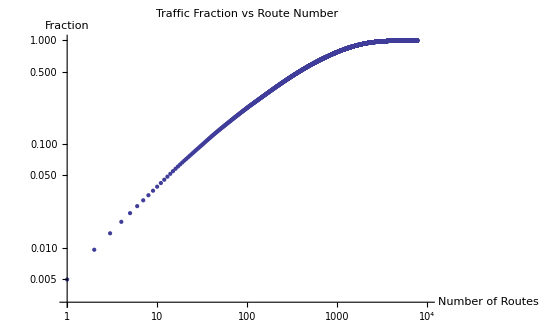

```mathematica
ListLogLogPlot[cumultable,PlotRange->{{1,10000},{.003,1}},PlotLabel->"Traffic Fraction vs Route Number",AxesLabel->{"Number of Routes", "Fraction"}]
```

```mathematica
FindFit[Table[{i,rankseatpairlist[[i,2]]},{i,7400}],rankseatpairlist[[1,2]] Exp[-b x^d]x^(c),{b,c,d},x,Method->NMinimize]
```

{b→0.0306946,c→-0.148013,d→0.600072}

```mathematica
1/.00136701
```

731.524

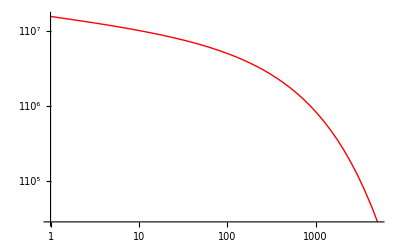

```mathematica
gc=LogLogPlot[rankseatpairlist[[1,2]]Exp[-.03069 x^.6] x^(-.148),{x,1,5000},PlotStyle->{Red,Thick}]
```

```mathematica
NIntegrate[rankseatpairlist[[1,2]]Exp[-.03069 x^.6] x^(-.148),{x,1,7000}]
```

3.35501×10^9

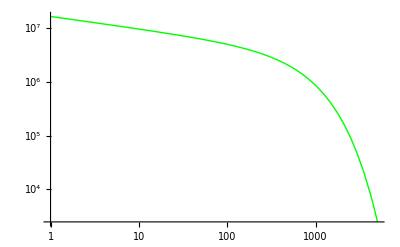

```mathematica
gb=LogLogPlot[rankseatpairlist[[1,2]]Exp[-.001367 x] x^(-.2294),{x,1,5000},PlotStyle->{Green,Thick}]
```

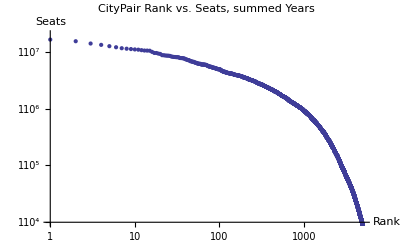

```mathematica
ga=ListLogLogPlot[Table[{i,rankseatpairlist[[i,2]]},{i,7463}],PlotRange->{{1,5000},{10^4,2 10^7}},PlotLabel->"CityPair Rank vs. Seats, summed Years",AxesLabel->{"Rank","Seats"}]
```

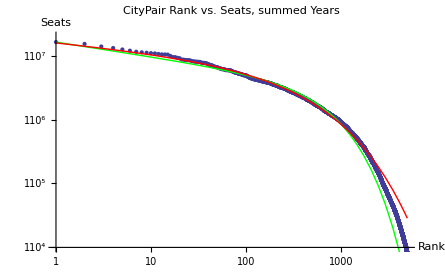

```mathematica
Show[ga,gb,gc]
```

```mathematica
rankseatpairlist[[1]]
```

{{HNL,OGG},16309046}

```mathematica
netairports=Table[Length[Union[Flatten[Table[rankseatpairlist[[i,1]],{i,j}]]]],{j,7750}];
```

```mathematica
netairports>>netairports;
```

```mathematica
linknodeplot=ListLogLogPlot[Table[{i,netairports[[i]]},{i,7750}],PlotLabel->"Number of Airports in Rank-Ordered City Pair Graph", AxesLabel->{"Top X Routes", "Number of Airports"},PlotRange->{{1,8000},{1,1200}}]
```

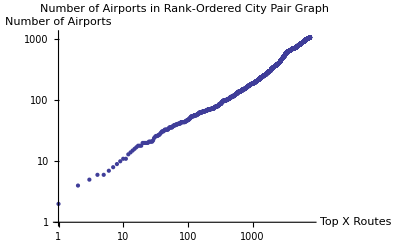

```mathematica
Log[100]/Log[800]//N
```

0.688921

```mathematica
FlatTable[rankseatpairlist[[i,1]],{i,20}]
```

{{HNL,OGG},{LAX,SFO},{LAS,LAX},{JFK,LAX},{HNL,LAX},{LAX,ORD},{LGA,ORD},{LAX,PHX},{BOS,LGA},{HNL,LIH},{LAS,PHX},{ATL,DFW},{ATL,MCO},{MSP,ORD},{DCA,LGA},{DEN,ORD},{EWR,ORD},{DFW,ORD},{ORD,SFO},{DAL,HOU}}

```mathematica
cumultable[[700]]//N
```

{700.,0.671536}

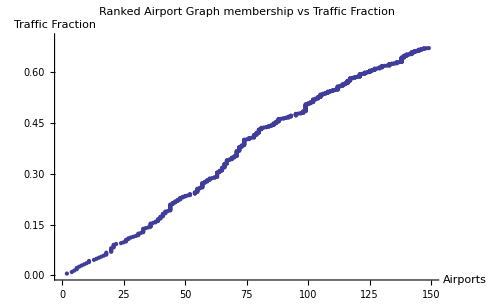

```mathematica
ListPlot[Table[{netairports[[i]],cumultable[[i,2]]},{i,700}],PlotRange->{{0,150},{0,0.7}},PlotLabel->"Ranked Airport Graph membership vs Traffic Fraction",AxesLabel->{"Airports","Traffic Fraction"}]
```

```mathematica
netairportsvstraffic=Table[{netairports[[i]],cumultable[[i,2]]},{i,7750}];
```

```mathematica
i=1;
While[netairportsvstraffic[[i,1]]<200,i++]
Print[netairportsvstraffic[[i,2]]//N]//N;
Print[i]
```

0.802374

1114

```mathematica
netairportsvstraffic[[379]]
```

{99,109541689/218947491}